## Forcing the frequencies

```mathematica
eq1:=X[r]+2G[r]-2A[r]==Subscript[γ, b]*r^i;
eq2:=X'[r]-2A'[r]-2G[r]A[r]+2G[r]X[r]-2 G[r]^2==X'[r]-2G'[r]+G[r]X[r]-G[r]A[r]-2 G[r]^2-A[r]^2+A[r]X[r];
eq3:=A[r]+X[r]-G[r]==Subscript[γ, f]*r^j;
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

2 A[r]+r^i γ_b==2 G[r]+X[r]

(A[r]-G[r]) (A[r]-X[r])+2 G'[r]==2 A'[r]

A[r]+X[r]==G[r]+r^j γ_f

```mathematica
Solve[eq1,X[r]]
```

{{X[r]→2 A[r]-2 G[r]+r^i γ_b}}

```mathematica
X[r_]:=2 A[r]-2 G[r]+r^i Subscript[γ, b];
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

True

(A[r]-G[r]) (A[r]-2 G[r]+r^i γ_b)+2 (A'[r]-G'[r])==0

3 A[r]+r^i γ_b==3 G[r]+r^j γ_f

```mathematica
Solve[eq3,A[r]]
```

{{A[r]→1/3 (3 G[r]-r^i γ_b+r^j γ_f)}}

```mathematica
A[r_]:=1/3 (3 G[r]-r^i Subscript[γ, b]+r^j Subscript[γ, f]);
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

True

2 r^(2 i) γ_b^2==(r^j γ_f (6 j-3 r G[r]+r^(1+j) γ_f)+r^i γ_b (-6 i+3 r G[r]+r^(1+j) γ_f))/r

True

```mathematica
FullSimplify[Solve[eq2,G[r]]]
```

{{G[r]→1/3 ((6 j)/r+r^j γ_f+2 r^i γ_b (1+(3 (i-j))/(r (r^i γ_b-r^j γ_f))))}}

```mathematica
G[r_]:=1/3 ((6 j)/r+r^j Subscript[γ, f]+2 r^i Subscript[γ, b] (1+(3 (i-j))/(r (r^i Subscript[γ, b]-r^j Subscript[γ, f]))));
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

True

True

True

```mathematica
FullSimplify[A[r]]
FullSimplify[G[r]]
FullSimplify[X[r]]
```

1/3 ((6 j)/r+2 r^j γ_f+r^i γ_b (1+(6 (i-j))/(r (r^i γ_b-r^j γ_f))))

1/3 ((6 j)/r+r^j γ_f+2 r^i γ_b (1+(3 (i-j))/(r (r^i γ_b-r^j γ_f))))

1/3 (r^i γ_b+2 r^j γ_f)

```mathematica
HC1:=B''[r]+B[r]*(X'[r]-2*A'[r])+B'[r]*(-2*A[r]+X[r]+2*G[r])-2*G[r]*B[r]*(A[r]-X[r]+G[r]);
HC2:=F''[r]+F[r]*(X'[r]-2*G'[r])+F'[r]*(A[r]+X[r]-G[r])+F[r]*(G[r]*(X[r]-A[r]-2G[r])-A[r]*(A[r]-X[r]))-G[r];
FullSimplify[HC1==0]
FullSimplify[HC2==0]
```

It is possible to solve the first equation for the special case i = j, however the second equation can not be solved without specifying the values of i = j

r^i γ_b B'[r]+B''[r]==1/9 B[r] (8 r^(2 i) γ_b^2+r^(-1+i) γ_b (75 i+8 r^(1+j) γ_f)+(2 (18 i (-1+4 i)+r^j γ_f (21 j r+r^(2+j) γ_f+(18 (i-j) (r^i γ_b (-1+7 i+j+3 r^(1+i) γ_b)-r^j (-1+4 i+4 j+3 r^(1+i) γ_b) γ_f))/((r^i γ_b-r^j γ_f)^2))))/r^2)

8 r^(1+3 i) F[r] γ_b^3+3 r^(2 i) γ_b^2 (2 r+F[r] (25 i+(36 (i-j)^2)/(r (r^i γ_b-r^j γ_f))))+3 r^(-1+i) γ_b (6 i r+12 ((-1+i) i+6 i j-3 j^2) F[r]-2 r^(2+2 j) F[r] γ_f^2-r^(1+j) γ_f (r-11 (i-2 j) F[r]+3 r F'[r])-3 r^2 F''[r])+r^(-1+j) γ_f (-18 j (r+(-2+8 j) F[r])-2 r^(2+2 j) F[r] γ_f^2+3 r^(1+j) γ_f (-14 j F[r]+r (-1+3 F'[r]))+9 r^2 F''[r])==0

```mathematica
i=j;
FullSimplify[HC1==0]
FullSimplify[DSolve[HC1==0,B[r],r]]
```

B[r] ((36 j (-1+4 j))/r+r^j (75 j γ_b+42 j γ_f+2 r^(1+j) (2 γ_b+γ_f)^2))==9 r (r^j γ_b B'[r]+B''[r])

{{B[r]→2^((9 j)/(2 (1+j))) ⅇ^(-1/6 r^(1+j) ((3 γ_b)/(1+j)+(√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))/(√((1+j)^2)))) r^(-j/2) (r^(1+j))^((9 j)/(2 (1+j))) (C[1] HypergeometricU[1/2 j (9/(1+j)+(53 γ_b+28 γ_f)/(√((1+j)^2) √(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))),(9 j)/(1+j),(r^(1+j) √(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))/(3 √((1+j)^2))]+C[2] LaguerreL[1/2 j (-9/(1+j)+(-53 γ_b-28 γ_f)/(√((1+j)^2) √(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))),8-9/(1+j),(r^(1+j) √(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))/(3 √((1+j)^2))])}}

```mathematica
FullSimplify[HC2==0]
```

(18 j (r+(-2+8 j) F[r]))/r+2 r^(1+2 j) F[r] (2 γ_b+γ_f)^2+3 r^j ((2 r+25 j F[r]) γ_b+γ_f (r+14 j F[r]-3 r F'[r]))==9 r F''[r]

### Checking i = j = 0

```mathematica
i=0;
j=0;
FullSimplify[HC1==0]
FullSimplify[DSolve[HC1==0,B[r],r]]
FullSimplify[HC2==0]
FullSimplify[DSolve[HC2==0,F[r],r]]
```

2 B[r] (2 γ_b+γ_f)^2==9 (γ_b B'[r]+B''[r])

{{B[r]→ⅇ^(-1/6 r (3 γ_b+√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))) (C[1]+ⅇ^(1/3 r √(41 γ_b^2+32 γ_b γ_f+8 γ_f^2)) C[2])}}

(2 γ_b+γ_f) (3+2 F[r] (2 γ_b+γ_f))==9 (γ_f F'[r]+F''[r])

{{F[r]→ⅇ^(-1/6 r (3 γ_f+√(32 γ_b^2+32 γ_b γ_f+17 γ_f^2))) (C[1]+ⅇ^(1/3 r √(32 γ_b^2+32 γ_b γ_f+17 γ_f^2)) C[2])-3/(4 γ_b+2 γ_f)}}

### Testing i = 1 and j = 0

```mathematica
i=1;
j=0;
FullSimplify[HC1==0]
FullSimplify[DSolve[HC1==0,B[r],r]]
FullSimplify[HC2==0]
FullSimplify[DSolve[HC2==0,F[r],r]]
```

1/9 B[r] (-2 γ_f^2+γ_b (33-8 r γ_f)+4 γ_b^2 (-2 r^2-27/(-r γ_b+γ_f)^2+(27 r)/(-r γ_b+γ_f)))+r γ_b B'[r]+B''[r]==0

{{B[r]→[r]}}

1/(r γ_b-γ_f)(8 r^4 F[r] γ_b^4+r^2 γ_b^3 (6 r+F[r] (75-8 r γ_f))+γ_f^2 (γ_f (3+2 F[r] γ_f-9 F'[r])-9 F''[r])+γ_b γ_f (-18+F[r] γ_f (-33+4 r γ_f)+18 r (γ_f F'[r]+F''[r]))-3 γ_b^2 (2 F[r] (-2+r γ_f) (9+r γ_f)+3 r (-2+r (γ_f (1+F'[r])+F''[r]))))==0

{{F[r]→[r]}}

### Testing i = 0 and j = 1

```mathematica
i=0;
j=1;
FullSimplify[HC1==0]
FullSimplify[DSolve[HC1==0,B[r],r]]
FullSimplify[HC2==0]
FullSimplify[DSolve[HC2==0,F[r],r]]
```

γ_b B'[r]+B''[r]==(2 B[r] (4 γ_b^4-γ_b^2 (33+4 r γ_b) γ_f+3 (18+r γ_b (4-r γ_b)) γ_f^2+r^2 (21+2 r γ_b) γ_f^3+r^4 γ_f^4))/(9 (γ_b-r γ_f)^2)

{{B[r]→[r]}}

1/(γ_b-r γ_f)(8 F[r] γ_b^4+γ_b^3 (6-8 r F[r] γ_f)+γ_f^2 (2 F[r] (3+r^2 γ_f) (18+r^2 γ_f)+3 r (6+r (r γ_f (1-3 F'[r])-3 F''[r])))+3 γ_b^2 (-γ_f (2 F[r] (11+r^2 γ_f)+3 r (1+F'[r]))-3 F''[r])+2 γ_b γ_f (-9+r γ_f (2 F[r] (6+r^2 γ_f)+9 r F'[r])+9 r F''[r]))==0

{{F[r]→[r]}}

### Testing i =1 and j = 1

```mathematica
i=1;
j=1;
FullSimplify[HC1==0]
FullSimplify[DSolve[HC1==0,B[r],r]]
FullSimplify[HC2==0]
FullSimplify[DSolve[HC2==0,F[r],r]]
```

B[r] (108/r+8 r^3 γ_b^2+2 r γ_f (21+r^2 γ_f)+r γ_b (75+8 r^2 γ_f))==9 r (r γ_b B'[r]+B''[r])

{{B[r]→1/(2 2^(1/4) r^(9/2))ⅇ^(-1/12 r^2 (3 γ_b+√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))) (r^2)^(3/4) (C[1] HypergeometricU[1/4 (-5+(53 γ_b+28 γ_f)/(√(41 γ_b^2+32 γ_b γ_f+8 γ_f^2))),-5/2,1/6 r^2 √(41 γ_b^2+32 γ_b γ_f+8 γ_f^2)]+C[2] LaguerreL[5/4-(53 γ_b+28 γ_f)/(4 √(41 γ_b^2+32 γ_b γ_f+8 γ_f^2)),-7/2,1/6 r^2 √(41 γ_b^2+32 γ_b γ_f+8 γ_f^2)])}}

18+(108 F[r])/r+r F[r] (8 r^2 γ_b^2+2 γ_f (21+r^2 γ_f)+γ_b (75+8 r^2 γ_f))+3 r^2 (2 γ_b+γ_f (1-3 F'[r]))==9 r F''[r]

$Aborted

### Testing i =-1 and j = 1

```mathematica
i=-1;
j=0;
FullSimplify[HC1==0]
FullSimplify[DSolve[HC1==0,B[r],r]]
FullSimplify[HC2==0]
FullSimplify[DSolve[HC2==0,F[r],r]]
```

(γ_b B'[r])/r+B''[r]==(B[r] (8 γ_b^4+2 r^4 γ_f^4-6 γ_b^2 (-10+r γ_f) (3+r γ_f)-γ_b^3 (75+8 r γ_f)+r γ_b γ_f (-72+r γ_f (33+4 r γ_f))))/(9 r^2 (γ_b-r γ_f)^2)

{{B[r]→[r]}}

1/(r (-γ_b+r γ_f))(8 F[r] γ_b^4+γ_b^3 (6 r-F[r] (75+8 r γ_f))+r^4 γ_f^2 (γ_f (3+2 F[r] γ_f-9 F'[r])-9 F''[r])+r γ_b γ_f (F[r] (-72+r γ_f (33+4 r γ_f))+18 r (1+r γ_f F'[r]+r F''[r]))-3 γ_b^2 (2 F[r] (-10+r γ_f) (3+r γ_f)+3 r (2+r (γ_f (1+F'[r])+F''[r]))))==0

{{F[r]→[r]}}

### Case i = j = -1

```mathematica
i=-1;
j=-1;
FullSimplify[HC1==0]
FullSimplify[DSolve[HC1==0,B[r],r]]
FullSimplify[HC2==0]
FullSimplify[DSolve[HC2==0,F[r],r]]
```

9 (γ_b B'[r]+r B''[r])==(B[r] (8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f)))/r

{{B[r]→r^(1/6 (3-3 γ_b-√(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √(-4-(9 (-1+γ_b)^2)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f))))) C[1]+r^(1/6 (3-3 γ_b+√(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √(-4-(9 (-1+γ_b)^2)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f))))) C[2]}}

9 (2+γ_f F'[r]+r F''[r])==6 γ_b+3 γ_f+(F[r] (8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f)))/r

{{F[r]→r^(1/6 (3-3 γ_f-√(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √((-729-32 γ_b^2+4 γ_b (75-8 γ_f)+(186-17 γ_f) γ_f)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f))))) C[1]+r^(1/6 (3-3 γ_f+√(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √((-729-32 γ_b^2+4 γ_b (75-8 γ_f)+(186-17 γ_f) γ_f)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f))))) C[2]-(3 r (-6+2 γ_b+γ_f))/(180+8 γ_b^2+γ_f (-51+2 γ_f)+γ_b (-75+8 γ_f))}}

```mathematica
B[r_]:=r^(1/6 (3-3 Subscript[γ, b]-√(-8 Subscript[γ, b]^2+Subscript[γ, b] (75-8 Subscript[γ, f])-2 (-15+Subscript[γ, f]) (-6+Subscript[γ, f])) √(-4-(9 (-1+Subscript[γ, b])^2)/(8 Subscript[γ, b]^2+2 (-15+Subscript[γ, f]) (-6+Subscript[γ, f])+Subscript[γ, b] (-75+8 Subscript[γ, f])))))Subscript[B, 1]+r^(1/6 (3-3 Subscript[γ, b]+√(-8 Subscript[γ, b]^2+Subscript[γ, b] (75-8 Subscript[γ, f])-2 (-15+Subscript[γ, f]) (-6+Subscript[γ, f])) √(-4-(9 (-1+Subscript[γ, b])^2)/(8 Subscript[γ, b]^2+2 (-15+Subscript[γ, f]) (-6+Subscript[γ, f])+Subscript[γ, b] (-75+8 Subscript[γ, f]))))) Subscript[B, 2];
F[r_]:=r^(1/6 (3-3 Subscript[γ, f]-√(-8 Subscript[γ, b]^2+Subscript[γ, b] (75-8 Subscript[γ, f])-2 (-15+Subscript[γ, f]) (-6+Subscript[γ, f])) √((-729-32 Subscript[γ, b]^2+4 Subscript[γ, b] (75-8 Subscript[γ, f])+(186-17 Subscript[γ, f]) Subscript[γ, f])/(8 Subscript[γ, b]^2+2 (-15+Subscript[γ, f]) (-6+Subscript[γ, f])+Subscript[γ, b] (-75+8 Subscript[γ, f]))))) Subscript[F, 1]+r^(1/6 (3-3 Subscript[γ, f]+√(-8 Subscript[γ, b]^2+Subscript[γ, b] (75-8 Subscript[γ, f])-2 (-15+Subscript[γ, f]) (-6+Subscript[γ, f])) √((-729-32 Subscript[γ, b]^2+4 Subscript[γ, b] (75-8 Subscript[γ, f])+(186-17 Subscript[γ, f]) Subscript[γ, f])/(8 Subscript[γ, b]^2+2 (-15+Subscript[γ, f]) (-6+Subscript[γ, f])+Subscript[γ, b] (-75+8 Subscript[γ, f]))))) Subscript[F, 2]-(3 r (-6+2 Subscript[γ, b]+Subscript[γ, f]))/(180+8 Subscript[γ, b]^2+Subscript[γ, f] (-51+2 Subscript[γ, f])+Subscript[γ, b] (-75+8 Subscript[γ, f]));
```

```mathematica
Rtt[r_]:=B'[r]+B[r]*(2*G[r]+X[r]-A[r]);
Rrr[r_]:=A'[r]+2G'[r]+A[r]A[r]+2G[r]G[r]-A[r]X[r]-2X[r]G[r];
Rthth[r_]:=F'[r]+F[r](A[r]+X[r])+1;
FullSimplify[Rtt[r]]
FullSimplify[Rrr[r]]
FullSimplify[Rthth[r]]
```

1/6 r^(1/6 (-3-3 γ_b-√(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √(-4-(9 (-1+γ_b)^2)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f))))) (B_1 (-9+5 γ_b+4 γ_f-√(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √(-4-(9 (-1+γ_b)^2)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f))))+r^(1/3 √(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √(-4-(9 (-1+γ_b)^2)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f)))) B_2 (-9+5 γ_b+4 γ_f+√(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √(-4-(9 (-1+γ_b)^2)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f)))))

(162+4 γ_b^2-2 γ_f (12+γ_f)-γ_b (57+2 γ_f))/(9 r^2)

(162+4 γ_b^2-2 γ_f (12+γ_f)-γ_b (57+2 γ_f))/(180+8 γ_b^2+γ_f (-51+2 γ_f)+γ_b (-75+8 γ_f))+1/6 r^(1/6 (-3-3 γ_f-√(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √((-729-32 γ_b^2+4 γ_b (75-8 γ_f)+(186-17 γ_f) γ_f)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f))))) F_1 (-9+4 γ_b+5 γ_f-√(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √((-729-32 γ_b^2+4 γ_b (75-8 γ_f)+(186-17 γ_f) γ_f)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f))))+1/6 r^(1/6 (-3-3 γ_f+√(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √((-729-32 γ_b^2+4 γ_b (75-8 γ_f)+(186-17 γ_f) γ_f)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f))))) F_2 (-9+4 γ_b+5 γ_f+√(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √((-729-32 γ_b^2+4 γ_b (75-8 γ_f)+(186-17 γ_f) γ_f)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f))))

## Auto-parallel curves

```mathematica
eq1t[τ_]:=t''[τ]+2*A[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t[τ]]
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*θ'[τ]^2+F[r[τ]]*ϕ'[τ]^2*Sin[θ]^2;
FullSimplify[eq1r[τ]]
eq1th[τ_]=θ''[τ]+2*G[r[τ]]*θ'[τ]*r'[τ]-Cos[θ]*Sin[θ]*ϕ'[τ]^2;
FullSimplify[eq1th[τ]]
eq1ph[τ_]=ϕ''[τ]+2*G[r[τ]]*ϕ'[τ]*r'[τ]+Cos[θ]/Sin[θ]*ϕ'[τ]*θ'[τ];
FullSimplify[eq1ph[τ]]
```

(2 (-6+γ_b+2 γ_f) r'[τ] t'[τ])/(3 r[τ])+t''[τ]

((γ_b+2 γ_f) r'[τ]^2)/(3 r[τ])+r[τ]^(1/6 (3-3 γ_b-√(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √(-4-(9 (-1+γ_b)^2)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f))))) B_1 t'[τ]^2+r[τ]^(1/6 (3-3 γ_b+√(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √(-4-(9 (-1+γ_b)^2)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f))))) B_2 t'[τ]^2+r[τ]^(1/6 (3-3 γ_f-√(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √((-729-32 γ_b^2+4 γ_b (75-8 γ_f)+(186-17 γ_f) γ_f)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f))))) F_1 (θ'[τ]^2+Sin[θ]^2 ϕ'[τ]^2)+r[τ]^(1/6 (3-3 γ_f+√(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √((-729-32 γ_b^2+4 γ_b (75-8 γ_f)+(186-17 γ_f) γ_f)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f))))) F_2 (θ'[τ]^2+Sin[θ]^2 ϕ'[τ]^2)-(3 r[τ] (-6+2 γ_b+γ_f) (θ'[τ]^2+Sin[θ]^2 ϕ'[τ]^2))/(180+8 γ_b^2+γ_f (-51+2 γ_f)+γ_b (-75+8 γ_f))+r''[τ]

(2 (-6+2 γ_b+γ_f) r'[τ] θ'[τ])/(3 r[τ])-Cos[θ] Sin[θ] ϕ'[τ]^2+θ''[τ]

(2 (-6+2 γ_b+γ_f) r'[τ] ϕ'[τ])/(3 r[τ])+Cot[θ] θ'[τ] ϕ'[τ]+ϕ''[τ]

Fixing θ=π/2

```mathematica
eq1t[τ_]:=t''[τ]+2*A[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t[τ]]
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]]
eq1ph[τ_]=ϕ''[τ]+2*G[r[τ]]*ϕ'[τ]*r'[τ];
FullSimplify[eq1ph[τ]]
```

(2 (-6+γ_b+2 γ_f) r'[τ] t'[τ])/(3 r[τ])+t''[τ]

((γ_b+2 γ_f) r'[τ]^2)/(3 r[τ])+r[τ]^(1/6 (3-3 γ_b-√(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √(-4-(9 (-1+γ_b)^2)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f))))) (B_1+r[τ]^(1/3 √(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √(-4-(9 (-1+γ_b)^2)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f)))) B_2) t'[τ]^2+(r[τ]^(1/6 (3-3 γ_f-√(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √((-729-32 γ_b^2+4 γ_b (75-8 γ_f)+(186-17 γ_f) γ_f)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f))))) F_1+r[τ]^(1/6 (3-3 γ_f+√(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √((-729-32 γ_b^2+4 γ_b (75-8 γ_f)+(186-17 γ_f) γ_f)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f))))) F_2-(3 r[τ] (-6+2 γ_b+γ_f))/(180+8 γ_b^2+γ_f (-51+2 γ_f)+γ_b (-75+8 γ_f))) ϕ'[τ]^2+r''[τ]

(2 (-6+2 γ_b+γ_f) r'[τ] ϕ'[τ])/(3 r[τ])+ϕ''[τ]

```mathematica
DSolve[(2 (-6+2 Subscript[γ, b]+Subscript[γ, f]) r'[τ] ϕ'[τ])/(3 r[τ])+ϕ''[τ]==0,ϕ[τ],τ]
```

{{ϕ[τ]→C[2]+C[1] r[K[1]]^(-2/3 (-6+2 γ_b+γ_f))K[1]1τ}}

```mathematica
D[Subscript[ϕ, 2]+Subscript[ϕ, 2] r[K[1]]^(-2/3 (-6+2 Subscript[γ, b]+Subscript[γ, f]))K[1]1τ,τ]
```

r[τ]^(-2/3 (-6+2 γ_b+γ_f)) ϕ_2

```mathematica
ϕ[τ_]:=Subscript[ϕ, 2]+Subscript[ϕ, 2] r[K[1]]^(-2/3 (-6+2 Subscript[γ, b]+Subscript[γ, f]))K[1]1τ;
eq1t[τ_]:=t''[τ]+2*A[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t[τ]]
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]]
eq1ph[τ_]=ϕ''[τ]+2*G[r[τ]]*ϕ'[τ]*r'[τ];
FullSimplify[eq1ph[τ]]
```

(2 (-6+γ_b+2 γ_f) r'[τ] t'[τ])/(3 r[τ])+t''[τ]

r[τ]^(-4/3 (-6+2 γ_b+γ_f)) (r[τ]^(1/6 (3-3 γ_f-√(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √((-729-32 γ_b^2+4 γ_b (75-8 γ_f)+(186-17 γ_f) γ_f)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f))))) F_1+r[τ]^(1/6 (3-3 γ_f+√(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √((-729-32 γ_b^2+4 γ_b (75-8 γ_f)+(186-17 γ_f) γ_f)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f))))) F_2-(3 r[τ] (-6+2 γ_b+γ_f))/(180+8 γ_b^2+γ_f (-51+2 γ_f)+γ_b (-75+8 γ_f))) ϕ_2^2+((γ_b+2 γ_f) r'[τ]^2)/(3 r[τ])+r[τ]^(1/6 (3-3 γ_b-√(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √(-4-(9 (-1+γ_b)^2)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f))))) (B_1+r[τ]^(1/3 √(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √(-4-(9 (-1+γ_b)^2)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f)))) B_2) t'[τ]^2+r''[τ]

0

```mathematica
DSolve[(2 (-6+Subscript[γ, b]+2 Subscript[γ, f]) r'[τ] t'[τ])/(3 r[τ])+t''[τ]==0,t[τ],τ]
```

{{t[τ]→C[2]+C[1] r[K[1]]^(-2/3 (-6+γ_b+2 γ_f))K[1]1τ}}

```mathematica
D[Subscript[t, 2]+Subscript[t, 1] r[K[1]]^(-2/3 (-6+Subscript[γ, b]+2 Subscript[γ, f]))K[1]1τ,τ]
```

r[τ]^(-2/3 (-6+γ_b+2 γ_f)) t_1

```mathematica
t[τ_]:=Subscript[t, 2]+Subscript[t, 1] r[K[1]]^(-2/3 (-6+Subscript[γ, b]+2 Subscript[γ, f]))K[1]1τ;
eq1t[τ_]:=t''[τ]+2*A[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t[τ]]
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]]
eq1ph[τ_]=ϕ''[τ]+2*G[r[τ]]*ϕ'[τ]*r'[τ];
FullSimplify[eq1ph[τ]]
```

0

r[τ]^(1/6 (51-11 γ_b-16 γ_f-√(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √(-4-(9 (-1+γ_b)^2)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f))))) (B_1+r[τ]^(1/3 √(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √(-4-(9 (-1+γ_b)^2)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f)))) B_2) t_1^2+r[τ]^(-4/3 (-6+2 γ_b+γ_f)) (r[τ]^(1/6 (3-3 γ_f-√(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √((-729-32 γ_b^2+4 γ_b (75-8 γ_f)+(186-17 γ_f) γ_f)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f))))) F_1+r[τ]^(1/6 (3-3 γ_f+√(-8 γ_b^2+γ_b (75-8 γ_f)-2 (-15+γ_f) (-6+γ_f)) √((-729-32 γ_b^2+4 γ_b (75-8 γ_f)+(186-17 γ_f) γ_f)/(8 γ_b^2+2 (-15+γ_f) (-6+γ_f)+γ_b (-75+8 γ_f))))) F_2-(3 r[τ] (-6+2 γ_b+γ_f))/(180+8 γ_b^2+γ_f (-51+2 γ_f)+γ_b (-75+8 γ_f))) ϕ_2^2+((γ_b+2 γ_f) r'[τ]^2)/(3 r[τ])+r''[τ]

0

A numerical computation

21/260 r[τ]^(31/3)+r[τ]^(44/3-(√233)/3)+r[τ]^(1/3 (44+√233))+r[τ]^(34/3-(√269)/3)+r[τ]^(1/3 (34+√269))-(5 r'[τ]^2)/(3 r[τ])+r''[τ]

{{r[τ]→InterpolatingFunction[…][τ]}}

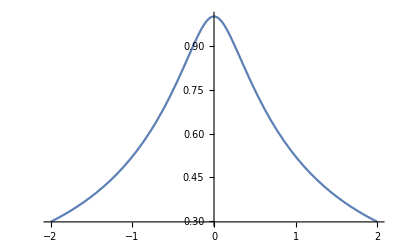

```mathematica
Subscript[γ, b]=1;Subscript[γ, f]=-3;
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]/.{Subscript[B, 1]->1,Subscript[B, 2]->1,Subscript[F, 1]->1,Subscript[F, 2]->1,Subscript[ϕ, 1]->1,Subscript[ϕ, 2]->1,Subscript[t, 1]->1,Subscript[t, 2]->1}]
s=NDSolve[{%==0,r[0]==1,r'[0]==0},r[τ],{τ,-2,2}]
Plot[r[τ]/.s,{τ,-2,2}]
```

```mathematica
FullSimplify[Rtt[r]]
FullSimplify[Rrr[r]]
FullSimplify[Rthth[r]]
```

1/3 r^(-1-(√233)/3) ((-8+√233) r^((2 √233)/3) B_1-(8+√233) B_2)

169/(9 r^2)

13/20+1/3 r^(1-(√269)/3) ((-10+√269) r^((2 √269)/3) F_1-(10+√269) F_2)

In the limit for the above special case leads to

```mathematica
Limit[Rtt[r],r->∞]
FullSimplify[Limit[Rrr[r],r->∞]]
Limit[Rthth[r],r->∞]
```

∞ B_1

0

∞ F_1

De Sitter metric

```mathematica
gtt[r_]:=-(1-(2*a)/r-b*r^2);
grr[r_]:=1/(1-(2*a)/r-b*r^2) ;
gthth[r_]:=r^2;
Limit[gtt[r],r->∞]
FullSimplify[Limit[grr[r],r->∞]]
Limit[gthth[r],r->∞]
```

b ∞

0

∞

Anti de Sitter

```mathematica
gtt[r_]:=-(1-a/r+b*r^2);
grr[r_]:=1/(1-a/r+b*r^2) ;
gthth[r_]:=r^2;
gthth[r_]:=r^2;
Limit[gtt[r],r->∞]
FullSimplify[Limit[grr[r],r->∞]]
Limit[gthth[r],r->∞]
```

b (-∞)

0

∞